# Smooth code for ORT

```mathematica
eta3 here represents etaxy
```

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,v11->2,v12->2.5,v21->1.8,v22->2.2,eta11->0.1,eta12->0.12,eta21->0.12,eta22->0.15,eta31->0.22,eta32->0.2,alfa->4,dz->2,th1->0,th2->Pi/6}
```

{v01→1.5,v02→2,v11→2,v12→2.5,v21→1.8,v22→2.2,eta11→0.1,eta12→0.12,eta21→0.12,eta22→0.15,eta31→0.22,eta32→0.2,alfa→4,dz→2,th1→0,th2→π/6}

```mathematica
z0=3
```

3

## k1

```mathematica
a=1/v01/.param;
```

```mathematica
b=1/v02/.param;
```

```mathematica
K=Piecewise[{{a,x<z0},{b,x≥z0}}]
```

Piecewise[{{0.666667, x<3}, {1/2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x<z0;
```

```mathematica
m1:=b/;x≥z0;
```

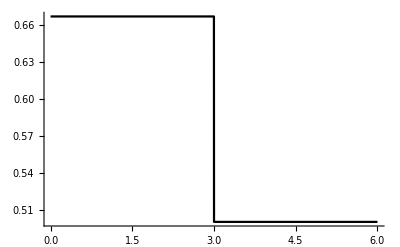

```mathematica
L1=Plot[m1,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
FF=K*E^(2*(x-z0)^2)/.param;
```

```mathematica
F1=(Integrate[FF,{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
S1=N[Integrate[a-F1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
S2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
A1=N[S1/S2];
```

```mathematica
CP=A1*E^(-alfa*(z+dz-z0)^2)/.param;
```

```mathematica
CPP=A1*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
k1=Simplify[F1-CPP+CP];
```

```mathematica
L2=Plot[k1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

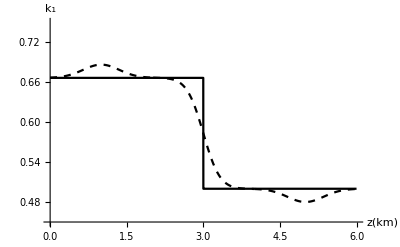

```mathematica
Show[{L1,L2},AxesOrigin->{0,0.45},PlotRange->{{0,6},{0.45,0.75}},AxesLabel->{Style["z(km)",FontSize->15],Style["k_1",FontSize->15]}]
```

```mathematica
(*HeavisideTheta*)
```

## k2

```mathematica
a1=(v11^2*Cos[th1]^2+v21^2*Sin[th1]^2)/v01/.param;
```

```mathematica
b1=(v12^2*Cos[th2]^2+v22^2*Sin[th2]^2)/v02/.param;
```

```mathematica
K1=Piecewise[{{a1,x<z0},{b1,x≥z0}}]
```

Piecewise[{{2.66667, x<3}, {2.94875, x≥3}, {0, True}}]

```mathematica
m2:=a1/;x<z0;
```

```mathematica
m2:=b1/;x≥z0;
```

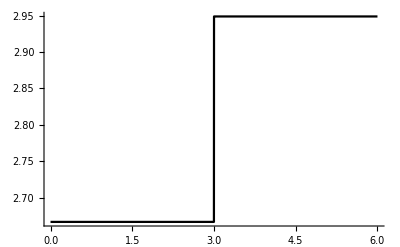

```mathematica
L11=Plot[m2,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Fn1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Sn1=N[Integrate[Fn1-a1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sn2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
An1=N[Sn1/Sn2];
```

```mathematica
k2=Fn1-An1*E^(-alfa*(z+dz-z0)^2)+An1*E^(-alfa*(z-dz-z0)^2)/.param;
```

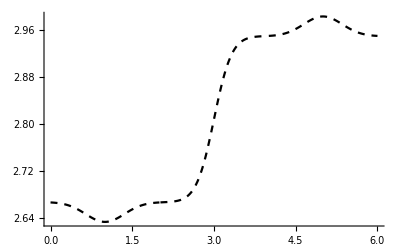

```mathematica
L12=Plot[k2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

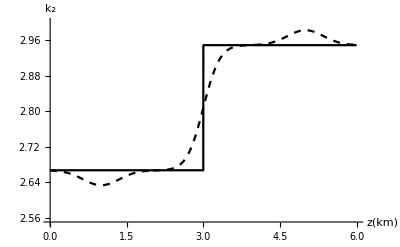

```mathematica
Show[{L11,L12},AxesOrigin->{0,2.55},PlotRange->{{0,6},{2.55,3.0}},AxesLabel->{Style["z(km)",FontSize->15],Style["k_2",FontSize->15]}]
```

## k3

```mathematica
a2=(v11^2*Sin[th1]^2+v21^2*Cos[th1]^2)/v01/.param;
```

```mathematica
b2=(v12^2*Sin[th2]^2+v22^2*Cos[th2]^2)/v02/.param;
```

```mathematica
K2=Piecewise[{{a2,x<z0},{b2,x≥z0}}]
```

Piecewise[{{2.16, x<3}, {2.59625, x≥3}, {0, True}}]

```mathematica
m3:=a2/;x<z0;
```

```mathematica
m3:=b2/;x≥z0;
```

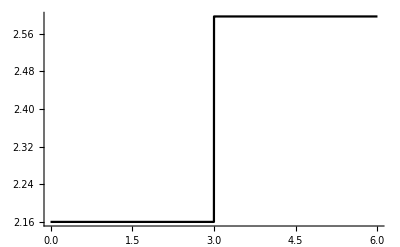

```mathematica
L21=Plot[m3,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Fn2=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Snn1=N[Integrate[Fn2-a2,{z,z0-dz/2/.param,z0}]]
```

0.0459873

```mathematica
Snn2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
An2=N[Snn1/Snn2]
```

0.052135

```mathematica
k3=Fn2-An2*E^(-alfa*(z+dz-z0)^2)+An2*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
L22=Plot[k3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

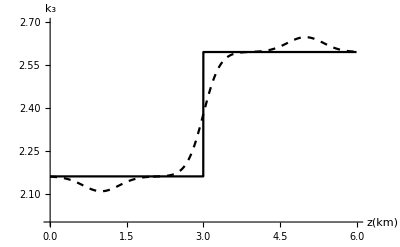

```mathematica
Show[{L21,L22},AxesOrigin->{0,2},PlotRange->{{0,6},{2,2.7}},AxesLabel->{Style["z(km)",FontSize->15],Style["k_3",FontSize->15]}]
```

## k4

```mathematica
a3=((v11^2-v21^2)*Sin[2*th1])/v01/.param;
```

```mathematica
b3=((v12^2-v22^2)*Sin[2*th2])/v02/.param;
```

```mathematica
K3=Piecewise[{{a3,x<z0},{b3,x≥z0}}]
```

Piecewise[{{0., x<3}, {0.610548, x≥3}, {0, True}}]

```mathematica
m4:=a3/;x<z0;
```

```mathematica
m4:=b3/;x≥z0;
```

```mathematica
Le1=Plot[m4,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Fn1e=(Integrate[K3*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Sne11=N[Integrate[Fn1e-a3,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sne12=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
Ane1=N[Sne11/Sne12];
```

```mathematica
k4=Fn1e-Ane1*E^(-alfa*(z+dz-z0)^2)+Ane1*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
Le2=Plot[k4,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

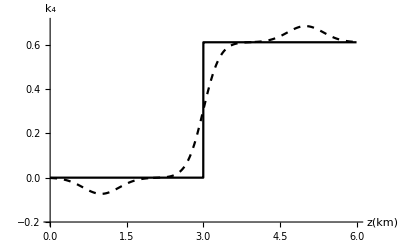

```mathematica
Show[{Le1,Le2},AxesOrigin->{0,-0.2},PlotRange->{{0,6},{-0.2,0.7}},AxesLabel->{Style["z(km)",FontSize->15],Style["k_4",FontSize->15]}]
```

## convert to the model parameters

```mathematica
V0=Simplify[1/k1];
```

```mathematica
Vnmo1=Simplify[Sqrt[(k2+k3+Sqrt[(k2-k3)^2+k4^2])/(2*k1)]];
```

```mathematica
Vnmo2=Simplify[Sqrt[(k2+k3-Sqrt[(k2-k3)^2+k4^2])/(2*k1)]];
```

```mathematica
THT=FullSimplify[ArcTan[k4/(k2-k3)]/2];
```

## unsmoothed model parameters v0

```mathematica
vel0:=v01/;z<z0;
```

```mathematica
vel0:=v02/;z≥z0;
```

```mathematica
p10=Plot[vel0/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p11=Plot[V0,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

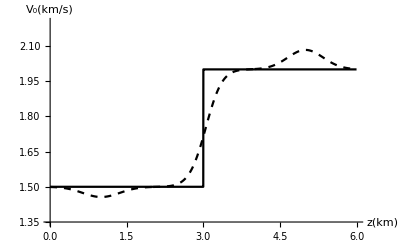

```mathematica
Show[{p10,p11},AxesOrigin->{0,1.35},PlotRange->{{0,6},{1.35,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_0(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v1

```mathematica
vel1:=v11/;z<z0;
```

```mathematica
vel1:=v12/;z≥z0;
```

```mathematica
p20=Plot[vel1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

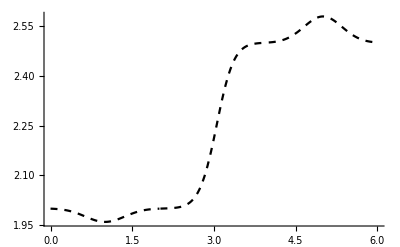

```mathematica
p21=Plot[Vnmo1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

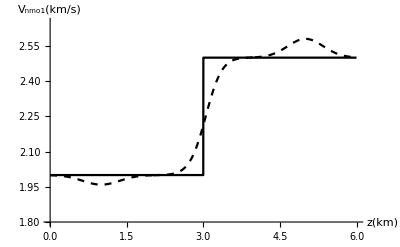

```mathematica
Show[{p20,p21},AxesOrigin->{0,1.8},PlotRange->{{0,6},{1.8,2.65}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo1(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v2

```mathematica
vel2:=v21/;z<z0;
```

```mathematica
vel2:=v22/;z≥z0;
```

```mathematica
p30=Plot[vel2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p31=Plot[Vnmo2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

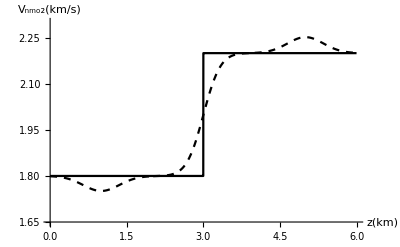

```mathematica
Show[{p30,p31},AxesOrigin->{0,1.65},PlotRange->{{0,6},{1.65,2.3}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo2(km/s)",FontSize->15]}]
```

## unsmoothed model parameters tht

```mathematica
t1:=th1*180/Pi/;z<z0;
```

```mathematica
t1:=th2*180/Pi/;z≥z0;
```

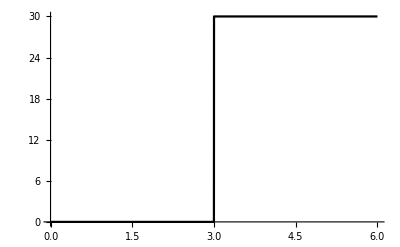

```mathematica
p40=Plot[t1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

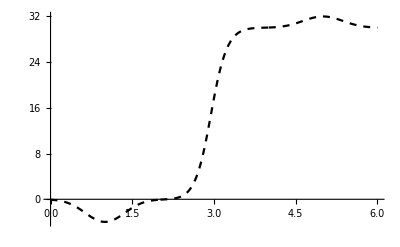

```mathematica
p41=Plot[THT*180/Pi,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

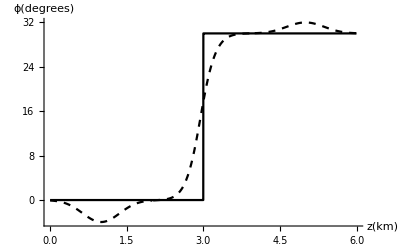

```mathematica
Show[{p40,p41},AxesOrigin->{0,-5},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["ϕ(degrees)",FontSize->15]}]
```

## Part 2

## composite Matrix 11

```mathematica
d11a=((1+8*eta11)*v11^4*Cos[th1]^4)/v01/.param;
```

```mathematica
d11b=((1+8*eta12)*v12^4*Cos[th2]^4)/v02/.param;
```

```mathematica
d11ab=Piecewise[{{d11a,x<z0},{d11b,x≥z0}}]
```

Piecewise[{{19.2, x<3}, {21.5332, x≥3}, {0, True}}]

```mathematica
SM1=(Integrate[d11ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM1a=N[Integrate[SM1-d11a,{z,z0-dz/2/.param,z0}]]
```

0.245955

```mathematica
SM1b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS11=SM1-N[SM1a/SM1b]*E^(-alfa*(z+dz-z0)^2)+N[SM1a/SM1b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

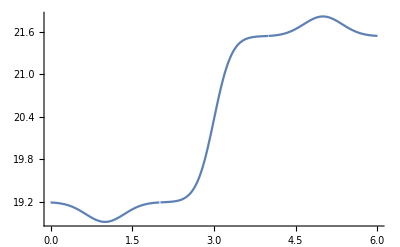

```mathematica
Plot[SMS11,{z,0,6}]
```

## composite Matrix 12

```mathematica
d12a=((1+8*eta21)*v21^4*Sin[th1]^4)/v01/.param;
```

```mathematica
d12b=((1+8*eta22)*v22^4*Sin[th2]^4)/v02/.param;
```

```mathematica
d12ab=Piecewise[{{d12a,x<z0},{d12b,x≥z0}}]
```

Piecewise[{{0., x<3}, {1.61051, x≥3}, {0, True}}]

```mathematica
SM2=(Integrate[d12ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM2a=N[Integrate[SM2-d12a,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM2b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS12=SM2-N[SM2a/SM2b]*E^(-alfa*(z+dz-z0)^2)+N[SM2a/SM2b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

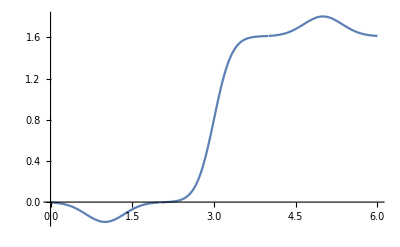

```mathematica
Plot[SMS12,{z,0,6}]
```

## composite Matrix 13

```mathematica
d13a=((1+4*eta31)*v11^2*v21^2*Sin[th1]^2*Cos[th1]^2)/v01/.param;
```

```mathematica
d13b=((1+4*eta32)*v12^2*v22^2*Sin[th2]^2*Cos[th2]^2)/v02/.param;
```

```mathematica
d13ab=Piecewise[{{d13a,x<z0},{d13b,x≥z0}}]
```

Piecewise[{{0., x<3}, {5.10469, x≥3}, {0, True}}]

```mathematica
SM3=(Integrate[d13ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM3a=N[Integrate[SM3-d13a,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM3b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS13=SM3-N[SM3a/SM3b]*E^(-alfa*(z+dz-z0)^2)+N[SM3a/SM3b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

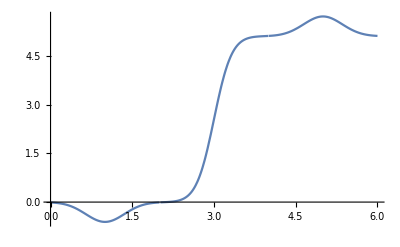

```mathematica
Plot[SMS13,{z,0,6}]
```

## composite Matrix 21

```mathematica
d21a=((1+8*eta11)*v11^4*Cos[th1]^2*Sin[2*th1])/v01/.param;
```

```mathematica
d21b=((1+8*eta12)*v12^4*Cos[th2]^2*Sin[2*th2])/v02/.param;
```

```mathematica
d21ab=Piecewise[{{d21a,x<z0},{d21b,x≥z0}}]
```

Piecewise[{{0., x<3}, {24.8644, x≥3}, {0, True}}]

```mathematica
SM4=(Integrate[d21ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM4a=N[Integrate[SM4-d21a,{z,z0-dz/2/.param,z0}]]
```

2.62108

```mathematica
SM4b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param]
```

0.882081

```mathematica
SMS21=SM4-N[SM4a/SM4b]*E^(-alfa*(z+dz-z0)^2)+N[SM4a/SM4b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

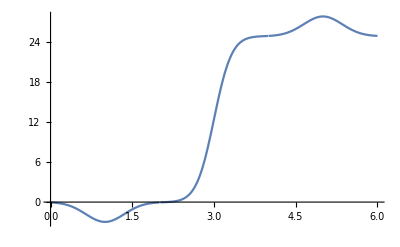

```mathematica
Plot[SMS21,{z,0,6}]
```

## composite Matrix 22

```mathematica
d22a=((1+8*eta21)*v21^4*Sin[th1]^2*Sin[2*th1])/v01/.param;
```

```mathematica
d22b=((1+8*eta22)*v22^4*Sin[th2]^2*Sin[2*th2])/v02/.param;
```

```mathematica
d22ab=Piecewise[{{d22a,x<z0},{d22b,x≥z0}}]
```

Piecewise[{{0., x<3}, {5.57897, x≥3}, {0, True}}]

```mathematica
SM5=(Integrate[d22ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM5a=N[Integrate[SM5-d22a,{z,z0-dz/2/.param,z0}]]
```

0.588107

```mathematica
SM5b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param]
```

0.882081

```mathematica
SMS22=SM5-N[SM5a/SM5b]*E^(-alfa*(z+dz-z0)^2)+N[SM5a/SM5b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

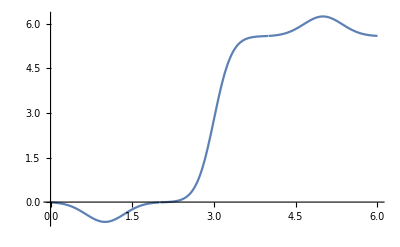

```mathematica
Plot[SMS22,{z,0,6}]
```

## composite Matrix 23

```mathematica
d23a=((1+4*eta31)*v11^2*v21^2*Sin[2*th1]*Cos[2*th1])/v01/.param;
```

```mathematica
d23b=((1+4*eta32)*v12^2*v22^2*Sin[2*th2]*Cos[2*th2])/v02/.param;
```

```mathematica
d23ab=Piecewise[{{d23a,x<z0},{d23b,x≥z0}}]
```

Piecewise[{{0., x<3}, {11.7888, x≥3}, {0, True}}]

```mathematica
SM6=(Integrate[d23ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM6a=N[Integrate[SM6-d23a,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM6b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS23=SM6-N[SM6a/SM6b]*E^(-alfa*(z+dz-z0)^2)+N[SM6a/SM6b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

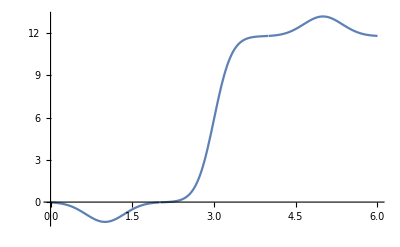

```mathematica
Plot[SMS23,{z,0,6}]
```

## composite Matrix 31

```mathematica
d31a=((1+8*eta11)*v11^4*Sin[2*th1]^2)/v01/.param;
```

```mathematica
d31b=((1+8*eta12)*v12^4*Sin[2*th2]^2)/v02/.param;
```

```mathematica
d31ab=Piecewise[{{d31a,x<z0},{d31b,x≥z0}}]
```

Piecewise[{{0., x<3}, {28.7109, x≥3}, {0, True}}]

```mathematica
SM7=(Integrate[d31ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM7a=N[Integrate[SM7-d31a,{z,z0-dz/2/.param,z0}]]
```

3.02656

```mathematica
SM7b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS31=SM7-N[SM7a/SM7b]*E^(-alfa*(z+dz-z0)^2)+N[SM7a/SM7b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

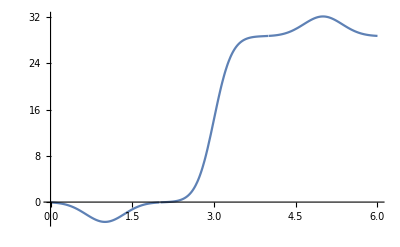

```mathematica
Plot[SMS31,{z,0,6}]
```

## composite Matrix 32

```mathematica
d32a=((1+8*eta21)*v21^4*Sin[2*th1]^2)/v01/.param;
```

```mathematica
d32b=((1+8*eta22)*v22^4*Sin[2*th2]^2)/v02/.param;
```

```mathematica
d32ab=Piecewise[{{d32a,x<z0},{d32b,x≥z0}}]
```

Piecewise[{{0., x<3}, {19.3261, x≥3}, {0, True}}]

```mathematica
SM8=(Integrate[d32ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM8a=N[Integrate[SM8-d32a,{z,z0-dz/2/.param,z0}]]
```

2.03726

```mathematica
SM8b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS32=SM8-N[SM8a/SM8b]*E^(-alfa*(z+dz-z0)^2)+N[SM8a/SM8b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

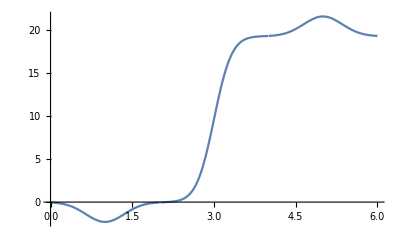

```mathematica
Plot[SMS32,{z,0,6}]
```

## composite Matrix 33

```mathematica
d33a=((1+4*eta31)*v11^2*v21^2*(1+3*Cos[4*th1]))/v01/.param;
```

```mathematica
d33b=((1+4*eta32)*v12^2*v22^2*(1+3*Cos[4*th2]))/v02/.param;
```

```mathematica
d33ab=Piecewise[{{d33a,x<z0},{d33b,x≥z0}}]
```

Piecewise[{{64.9728, x<3}, {-13.6125, x≥3}, {0, True}}]

```mathematica
SM9=(Integrate[d33ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM9a=N[Integrate[d33a-SM9,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM9b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS33=SM9+N[SM9a/SM9b]*E^(-alfa*(z+dz-z0)^2)-N[SM9a/SM9b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

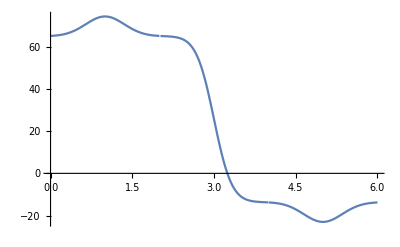

```mathematica
Plot[SMS33,{z,0,6}]
```

## composite Matrix 41

```mathematica
d41a=((1+8*eta11)*v11^4*Sin[2*th1]*Sin[th1]^2)/v01/.param;
```

```mathematica
d41b=((1+8*eta12)*v12^4*Sin[2*th2]*Sin[th2]^2)/v02/.param;
```

```mathematica
d41ab=Piecewise[{{d41a,x<z0},{d41b,x≥z0}}]
```

Piecewise[{{0., x<3}, {8.28813, x≥3}, {0, True}}]

```mathematica
SM10=(Integrate[d41ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM10a=N[Integrate[SM10-d41a,{z,z0-dz/2/.param,z0}]]
```

0.873693

```mathematica
SM10b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS41=SM10-N[SM10a/SM10b]*E^(-alfa*(z+dz-z0)^2)+N[SM10a/SM10b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

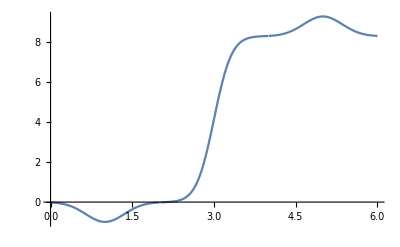

```mathematica
Plot[SMS41,{z,0,6}]
```

## composite Matrix 42

```mathematica
d42a=((1+8*eta21)*v21^4*Sin[2*th1]*Cos[th1]^2)/v01/.param;
```

```mathematica
d42b=((1+8*eta22)*v22^4*Sin[2*th2]*Cos[th2]^2)/v02/.param;
```

```mathematica
d42ab=Piecewise[{{d42a,x<z0},{d42b,x≥z0}}]
```

Piecewise[{{0., x<3}, {16.7369, x≥3}, {0, True}}]

```mathematica
SM11=(Integrate[d42ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM11a=N[Integrate[SM11-d42a,{z,z0-dz/2/.param,z0}]]
```

1.76432

```mathematica
SM11b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS42=SM11-N[SM11a/SM11b]*E^(-alfa*(z+dz-z0)^2)+N[SM11a/SM11b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

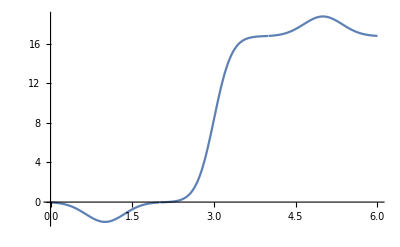

```mathematica
Plot[SMS42,{z,0,6}]
```

## composite Matrix 43

```mathematica
d43a=((1+4*eta31)*v11^2*v21^2*Sin[2*th1]*Cos[2*th1])/v01/.param;
```

```mathematica
d43b=((1+4*eta32)*v12^2*v22^2*Sin[2*th2]*Cos[2*th2])/v02/.param;
```

```mathematica
d43ab=Piecewise[{{d43a,x<z0},{d43b,x≥z0}}]
```

Piecewise[{{0., x<3}, {11.7888, x≥3}, {0, True}}]

```mathematica
SM12=(Integrate[d43ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM12a=N[Integrate[SM12-d43a,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM12b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS43=SM12-N[SM12a/SM12b]*E^(-alfa*(z+dz-z0)^2)+N[SM12a/SM12b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
Plot[SMS43,{z,0,6}]
```

-Graphics-

## composite Matrix 51

```mathematica
d51a=((1+8*eta11)*v11^4*Sin[th1]^4)/v01/.param;
```

```mathematica
d51b=((1+8*eta12)*v12^4*Sin[th2]^4)/v02/.param;
```

```mathematica
d51ab=Piecewise[{{d51a,x<z0},{d51b,x≥z0}}]
```

Piecewise[{{0., x<3}, {2.39258, x≥3}, {0, True}}]

```mathematica
SM13=(Integrate[d51ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM13a=N[Integrate[SM13-d51a,{z,z0-dz/2/.param,z0}]]
```

0.252214

```mathematica
SM13b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS51=SM13-N[SM13a/SM13b]*E^(-alfa*(z+dz-z0)^2)+N[SM13a/SM13b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

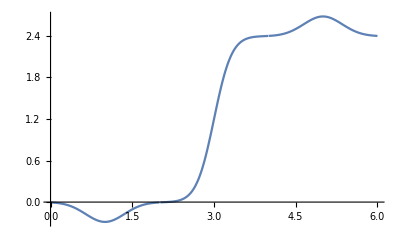

```mathematica
Plot[SMS51,{z,0,6}]
```

## composite Matrix 52

```mathematica
d52a=((1+8*eta21)*v21^4*Cos[th1]^4)/v01/.param;
```

```mathematica
d52b=((1+8*eta22)*v22^4*Cos[th2]^4)/v02/.param;
```

```mathematica
d52ab=Piecewise[{{d52a,x<z0},{d52b,x≥z0}}]
```

Piecewise[{{13.7169, x<3}, {14.4946, x≥3}, {0, True}}]

```mathematica
SM14=(Integrate[d52ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM14a=N[Integrate[SM14-d52a,{z,z0-dz/2/.param,z0}]];
```

```mathematica
SM14b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
SMS52=SM14-N[SM14a/SM14b]*E^(-alfa*(z+dz-z0)^2)+N[SM14a/SM14b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

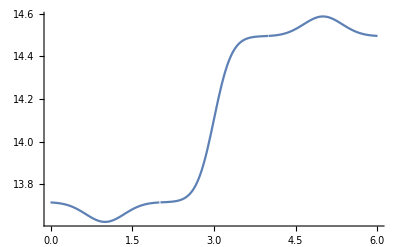

```mathematica
Plot[SMS52,{z,0,6}]
```

## composite Matrix 53

```mathematica
d53a=((1+4*eta31)*v11^2*v21^2*Sin[th1]^2*Cos[th1]^2)/v01/.param;
```

```mathematica
d53b=((1+4*eta32)*v12^2*v22^2*Sin[th2]^2*Cos[th2]^2)/v02/.param;
```

```mathematica
d53ab=Piecewise[{{d53a,x<z0},{d53b,x≥z0}}]
```

Piecewise[{{0., x<3}, {5.10469, x≥3}, {0, True}}]

```mathematica
SM15=(Integrate[d53ab*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
SM15a=N[Integrate[SM15-d53a,{z,z0-dz/2/.param,z0}]]
```

0.53811

```mathematica
SM15b=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param]
```

0.882081

```mathematica
SMS53=SM15-N[SM15a/SM15b]*E^(-alfa*(z+dz-z0)^2)+N[SM15a/SM15b]*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
Plot[SMS53,{z,0,6}]
```

-Graphics-

## part 3

## element of matrix D

```mathematica
D11=(V0*SMS11-Vnmo1^4*Cos[THT]^4)/4;
```

```mathematica
D12=(V0*SMS12-Vnmo2^4*Sin[THT]^4)/4;
```

```mathematica
D13=(V0*SMS13-Vnmo1^2*Vnmo2^2*Sin[THT]^2*Cos[THT]^2)/2;
```

```mathematica
D21=(V0*SMS21-Vnmo1^4*Cos[THT]^2*Sin[2*THT])/4;
```

```mathematica
D22=(-V0*SMS22+Vnmo2^4*Sin[THT]^2*Sin[2*THT])/4;
```

```mathematica
D23=(-V0*SMS23+Vnmo1^2*Vnmo2^2*Cos[2*THT]*Sin[2*THT])/4;
```

```mathematica
D31=3*(V0*SMS31-Vnmo1^4*Sin[2*THT]^2)/4;
```

```mathematica
D32=3*(V0*SMS32-Vnmo2^4*Sin[2*THT]^2)/4;
```

```mathematica
D33=(V0*SMS33-Vnmo1^2*Vnmo2^2*(1+3*Cos[4*THT]))/4;
```

```mathematica
D41=(V0*SMS41-Vnmo1^4*Sin[THT]^2*Sin[2*THT])/4;
```

```mathematica
D42=(-V0*SMS42+Vnmo2^4*Cos[THT]^2*Sin[2*THT])/4;
```

```mathematica
D43=(V0*SMS43-Vnmo1^2*Vnmo2^2*Cos[2*THT]*Sin[2*THT])/4;
```

```mathematica
D51=(V0*SMS51-Vnmo1^4*Sin[THT]^4)/4;
```

```mathematica
D52=(V0*SMS52-Vnmo2^4*Cos[THT]^4)/4;
```

```mathematica
D53=(V0*SMS53-Vnmo1^2*Vnmo2^2*Sin[THT]^2*Cos[THT]^2)/2;
```

```mathematica
MRD={{D11,D12,D13},{D21,D22,D23},{D31,D32,D33},{D41,D42,D43},{D51,D52,D53}};
```

## matrix U

```mathematica
(*U={{2*Cos[THT]^4,2*Sin[THT]^4,2*Sin[THT]^2*Cos[THT]^2},{2*Cos[THT]^2*Sin[2*THT],-2*Sin[THT]^2*Sin[2*THT],-Cos[2*THT]*Sin[2*THT]},{6*Sin[2*THT]^2,6*Sin[2*THT]^2,1+3*Cos[4*THT]},{2*Sin[THT]^2*Sin[2*THT],-2*Cos[THT]^2*Sin[2*THT],Cos[2*THT]*Sin[2*THT]},{2*Sin[THT]^4,2*Cos[THT]^4,2*Sin[THT]^2*Cos[THT]^2}};*)
```

```mathematica
F={{(2 Cos[THT]^4 (-30+69 Cos[2 THT]-46 Cos[4 THT]+23 Cos[6 THT]))/(41+23 Cos[8 THT]),(2 Cos[THT]^3 (9+23 Cos[2 THT]-23 Cos[4 THT]+23 Cos[6 THT]) Sin[THT])/(41+23 Cos[8 THT]),(4 Sin[2 THT]^2)/(41+23 Cos[8 THT]),-((5 Cos[THT]+23 (2 Cos[3 THT]+2 Cos[5 THT]+Cos[7 THT])) Sin[THT]^3)/(41+23 Cos[8 THT]),-(2 (30+69 Cos[2 THT]+46 Cos[4 THT]+23 Cos[6 THT]) Sin[THT]^4)/(41+23 Cos[8 THT])},{-(2 (30+69 Cos[2 THT]+46 Cos[4 THT]+23 Cos[6 THT]) Sin[THT]^4)/(41+23 Cos[8 THT]),((5 Cos[THT]+23 (2 Cos[3 THT]+2 Cos[5 THT]+Cos[7 THT])) Sin[THT]^3)/(41+23 Cos[8 THT]),(4 Sin[2 THT]^2)/(41+23 Cos[8 THT]),-(2 Cos[THT]^3 (9+23 Cos[2 THT]-23 Cos[4 THT]+23 Cos[6 THT]) Sin[THT])/(41+23 Cos[8 THT]),(2 Cos[THT]^4 (-30+69 Cos[2 THT]-46 Cos[4 THT]+23 Cos[6 THT]))/(41+23 Cos[8 THT])},{-(8 Cos[THT]^2 (-1+23 Cos[4 THT]) Sin[THT]^2)/(41+23 Cos[8 THT]),((Cos[THT]+Cos[3 THT]) (-27+23 Cos[4 THT]) Sin[THT])/(41+23 Cos[8 THT]),(4 (1+3 Cos[4 THT]))/(41+23 Cos[8 THT]),-((Cos[THT]+Cos[3 THT]) (-27+23 Cos[4 THT]) Sin[THT])/(41+23 Cos[8 THT]),-(8 Cos[THT]^2 (-1+23 Cos[4 THT]) Sin[THT]^2)/(41+23 Cos[8 THT])}};
```

```mathematica
G=F.MRD;
```

```mathematica
S=Transpose[{{1/Vnmo1^4,1/Vnmo2^4,1/(Vnmo1^2*Vnmo2^2)}}];
```

```mathematica
{{ETA1},{ETA2},{ETAxy}}=G.S;
```

```mathematica
ETA3=((((1+2*ETA1)*(1+2*ETA2))/(1+ETAxy)^2)-1)/2;
```

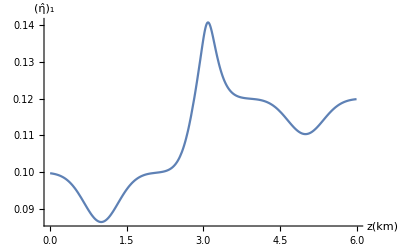
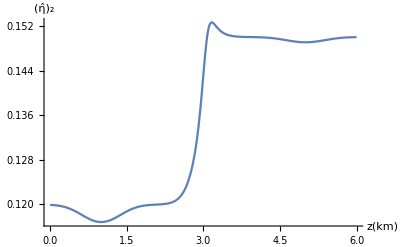
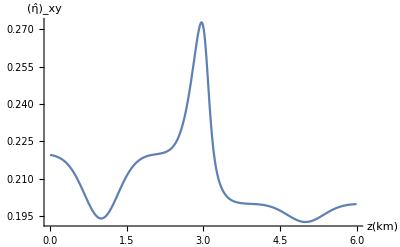
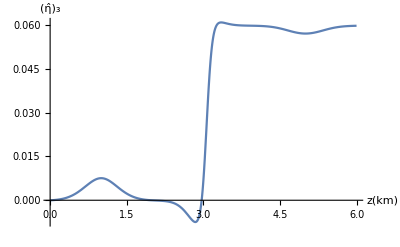

```mathematica
{Plot[ETA1,{z,0,6},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_1",FontSize->15]}],Plot[ETA2,{z,0,6},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_2",FontSize->15]}],Plot[ETAxy,{z,0,6},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_xy",FontSize->15]}],Plot[ETA3,{z,0,6},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_3",FontSize->15]}]}
```

## compare with unelipticall param

```mathematica
et1:=eta11/;z<z0;
```

```mathematica
et1:=eta12/;z≥z0;
```

```mathematica
p40a=Plot[et1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
et2:=eta21/;z<z0;
```

```mathematica
et2:=eta22/;z≥z0;
```

```mathematica
p50=Plot[et2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p51=Plot[ETA2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
et3:=eta31/;z<z0;
```

```mathematica
et3:=eta32/;z≥z0;
```

```mathematica
p60=Plot[et3/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p61=Plot[ETAxy,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

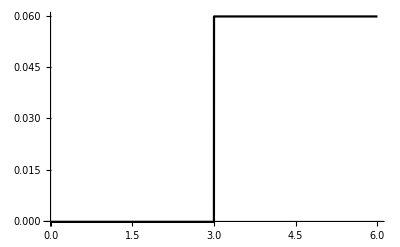

```mathematica
p70=Plot[1/2 (-1+((1+2 et1) (1+2 et2))/(1+et3)^2)/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
p71=Plot[ETA3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

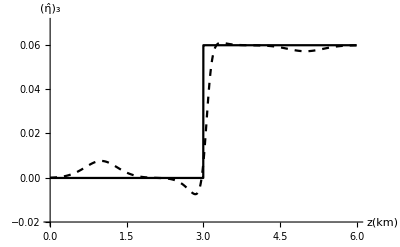

```mathematica
Show[{p70,p71},AxesOrigin->{0,-0.02},PlotRange->{{0,6},{-0.02,0.07}},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_3",FontSize->15]}]
```

## unsmoothed traveltime

```mathematica
Xpp=Sum[(px vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
Ypp=Sum[(py (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
Tpp=Sum[((py^2 (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2+px^2 vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2+(1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2) (1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2)) *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
Tpp1=Sum[((py^2 (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2+px^2 vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2+(1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2) (1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2)) *0.01)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.01}];
```

```mathematica
ddd=Abs[Tpp1-Tpp];
```

## for the traveltime error

## traveltime error

#### For PTS

```mathematica
f11=1-(1+2*ETA1)*px^2*Vnmo1^2-(1+2*ETA2)*py^2*Vnmo2^2+((1+2*ETA1)*(1+2*ETA2)-(1+ETAxy)^2)*px^2*py^2*Vnmo1^2*Vnmo2^2;
```

```mathematica
f22=1-2*ETA1*px^2*Vnmo1^2-2*ETA2*py^2*Vnmo2^2+(4*ETA1*ETA2-ETAxy^2)*px^2*py^2*Vnmo1^2*Vnmo2^2;
```

```mathematica
Th11=((2*ETA1-ETAxy)*px^2*Vnmo1^2-1)^2;
```

```mathematica
Th22=((2*ETA2-ETAxy)*py^2*Vnmo2^2-1)^2;
```

```mathematica
Xppp=Sum[((px*Vnmo1^2*0.001*Th22)/(f22^(3/2)*f11^(1/2)*V0))/.param,{z,0,6,0.001}];
```

```mathematica
Yppp=Sum[(py*Vnmo2^2*0.001*Th11)/(f22^(3/2)*f11^(1/2)*V0)/.param,{z,0,6,0.001}];
```

```mathematica
Tppp=Sum[(0.001*(f11*f22+px^2*Vnmo1^2*Th22+py^2*Vnmo2^2*Th11))/(f22^(3/2)*f11^(1/2)*V0)/.param,{z,0,6,0.001}];
```

```mathematica
DT=Abs[Tpp-Tppp];
```

```mathematica
ParametricPlot3D[{Xpp/6,Ypp/6,DT},{px,0,0.5},{py,0,0.5},PlotRange->{{0,1},{0,1},{0,0.0085}},AxesLabel->{Style["x/z   ",FontSize->15],Style["y/z   ",FontSize->15],Style["|ΔT|(s)      ",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<5&&Abs[v]<5&&0<w<0.02],ColorFunction->(ColorData["TemperatureMap",#3*10]&)]
```

-Graphics3D-

```mathematica
CRT=DT/.px->0/.py->0;
```

```mathematica
ParametricPlot3D[{Xpp/6,Ypp/6,Abs[DT-CRT]},{px,0,0.5},{py,0,0.5},PlotRange->{{0,1},{0,1},{0,0.0085}},AxesLabel->{Style["x/z   ",FontSize->15],Style["y/z   ",FontSize->15],Style["|ΔT|(s)      ",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<5&&Abs[v]<5&&0<w<0.02],ColorFunction->(ColorData["TemperatureMap",#3*10]&)]
```

-Graphics3D-

```mathematica
DumpSave["fx.mx",Xppp];
```

```mathematica
DumpSave["fx.mx",Yppp];
```

```mathematica
DumpSave["ft.mx",Tppp];
```

```mathematica
DumpSave["fdt.mx",DT];
```